```mathematica
DiffurStruc[func_,arg_,cprFunc_,ccur_]:={func'[arg]-ccur-cprFunc[func[arg]]==0};
DiffurIni[func_,InitialPoint_,InitialValue_]:={func[InitialPoint]==InitialValue};
Diffur[func_,arg_,cprFunc_,ccur_,InitialPoint_,InitialValue_]:=Flatten[
{DiffurStruc[func,arg,cprFunc,ccur],DiffurIni[func,InitialPoint,InitialValue]}];
CommonCPR[ccur_, cprFunc_, InitialPoint_,InitialValue_, {arg_,lowRange_,upperRange_}]:=
NDSolve[Diffur[γ,arg,cprFunc,ccur,InitialPoint,InitialValue],γ[arg],{arg,lowRange,upperRange}];
solution[ccur_, cprFunc_,tmax_]:=Flatten[γ[t]/.CommonCPR[ccur, cprFunc,0,0,{t,0,tmax}]];
```

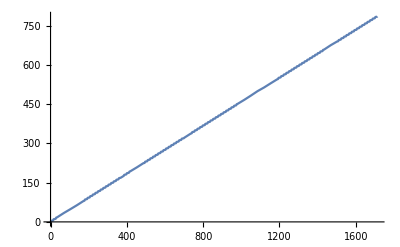

```mathematica
j=1.1;
Plot[Evaluate[solution[1.1,Sin,300(2π)/j]],{t,0,300(2π)/j}]
```

```mathematica
Clear[j];
v[j_?NumericQ,cprFunc_]:=((solution[j,cprFunc,300π]/.t->300π)⟦1⟧)/(300π)
```

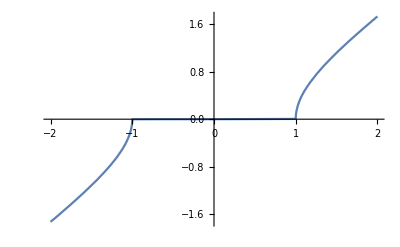

-1.00824+1.0069 j

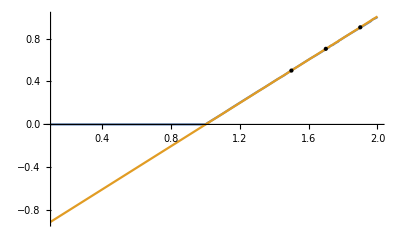

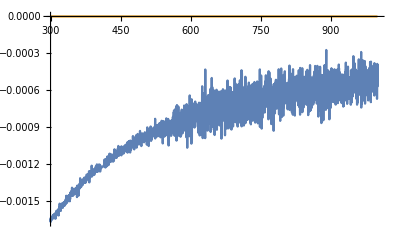

```mathematica
(*Классическая ВАХ для гармонической ток фазы*)
Plot[v[j,Sin],{j,-2,2}]
(*Попытка удостовериться в корневом поведении вблизи нуля (Если имеем зависимость вида √(j^2+const), то должна получится прямая)*)
fit=Fit[Table[{j,v[√j,Sin]^2},{j,1.5,2,0.2}],{1,j},j]
Plot[{v[√j,Sin]^2,fit},{j,0.1,2},Epilog->{PointSize[Medium],Point[Table[{j,v[√j,Sin]^2},{j,1.5,2,0.2}]]}]
(*Проверка на избыточный ток*)
Plot[{v[j]-j,0},{j,300,1000}]
```

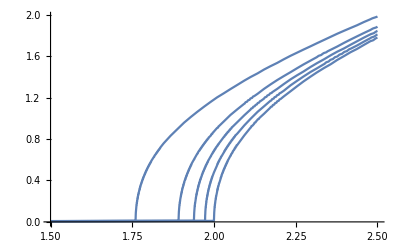

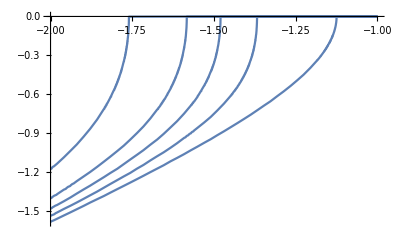

```mathematica
(*Строим ВАХ для различных ток-фазовых соотношений*)
cprFunc[a_,c_,d_,f_,j_]:=
{v[j,(Sin[#]+a Sin[c#]+d Sin[f#])&],
v[j,(Sin[#]+a Sin[c#+π/6]+d Sin[f#+π/6])&],
v[j,(Sin[#]+a Sin[c#+π/4]+d Sin[f#+π/4])&],
v[j,(Sin[#]+a Sin[c#+π/3]+d Sin[f#+π/3])&],
v[j,(Sin[#]+a Sin[c#+π/2]+d Sin[f#+π/2])&]};
Plot[cprFunc[1,2,0,3,j],{j,1.5,2.5}]
Plot[cprFunc[1,2,0,3,j],{j,-1,-2}]
```

```mathematica
(*Видно что зависимость от потока на больших токах исчезает (первые три рисунка абсолютно идентичны, а исходные выражения отличаются фазой)*)
```

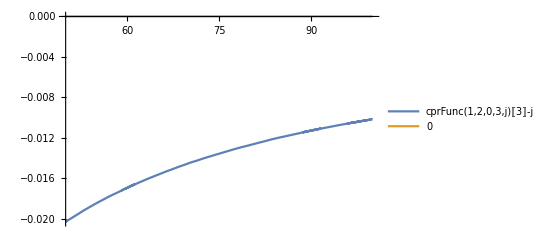

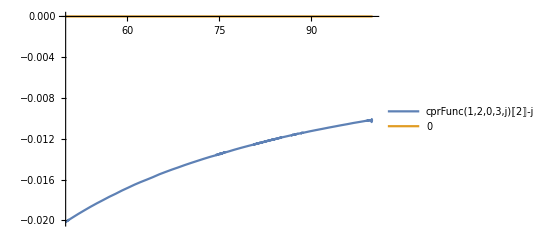

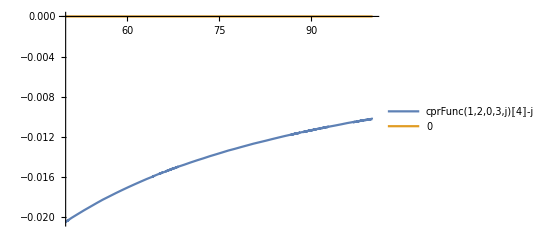

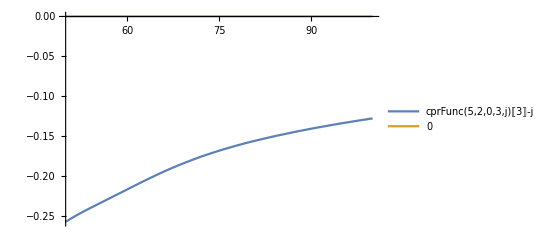

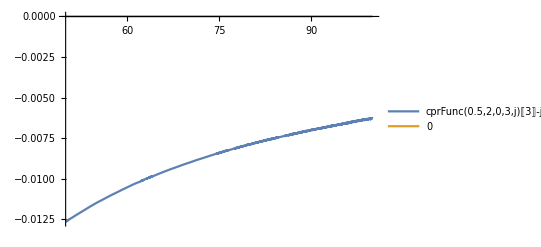

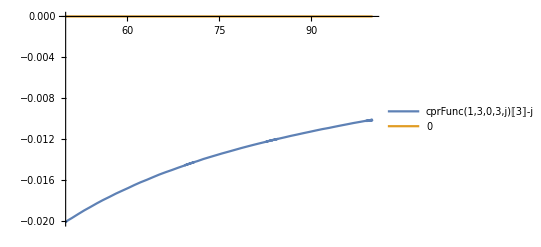

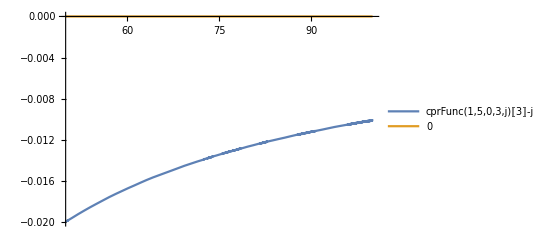

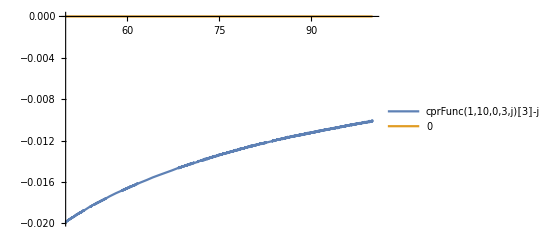

-Graphics-

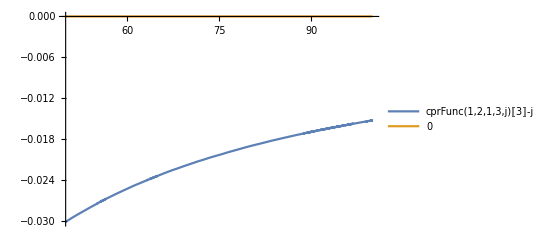

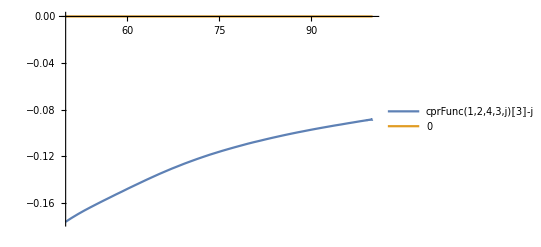

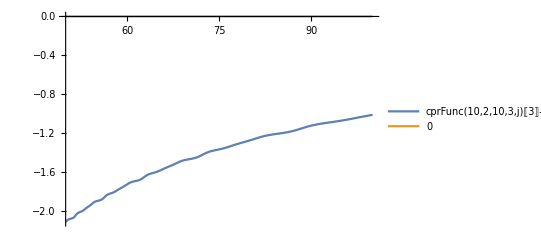

```mathematica
Plot[{cprFunc[1,2,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,2,0,3,j]⟦2⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,2,0,3,j]⟦4⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[5,2,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[0.5,2,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,3,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,5,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,10,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,10,0,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,2,1,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[1,2,4,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
Plot[{cprFunc[10,2,10,3,j]⟦3⟧-j,0},{j,50,100},PlotLegends->"Expressions"]
```

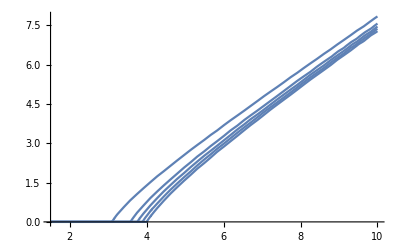

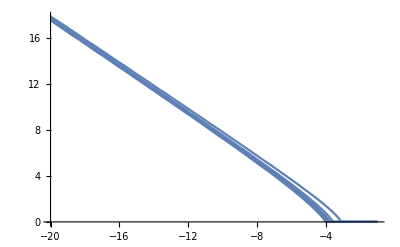

```mathematica
(*Попытка обнаружить корневое поведение. Врядли что-то можно сказать, кажется что прямая немного изогнута в окрестности крит тока.*)
Plot[cprFunc[1,2,0,3,√j]^2,{j,1.5,10}]
Plot[cprFunc[1,2,0,3,√Abs[j]]^2,{j,-1,-20}]
```

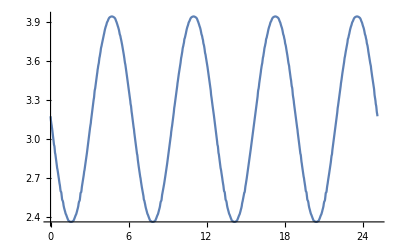

```mathematica
Clear[a];a=1;
Clear[c];c=2;
Clear[d];d=0;
Clear[f];f=3;
Clear[ϕ];
(*Зато так получилось построить красивую зависимость крит тока от потока. Надо проверить как оно согласуется с определением крит. тока через экстремумы ток-фазы*)
Plot[Fit[Table[v[√Abs[j],(Sin[#]+a Sin[c#+ϕ]+d Sin[f#+ϕ])&]^2,{j,6,10,0.5}],{1,j},j]/.j->0,{ϕ,0,8π}]
```

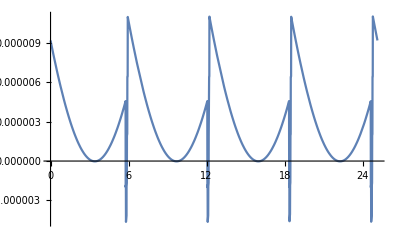

```mathematica
(*Тут получилась такая некрасивая картинка, потому что взята неудачная выборка точек для фиттинга. При том способе преобразования графика к прямой линии, который тут использован, значение крит тока после преобразования увеличивается. Я не учел этого и существенная часть точек попала в "бездиссипативный" участок кривой ниже крит. тока. Поэтому фиттинг дает неадекватные результаты на шесть порядков ниже чем в предыдущем случае.*)  
Clear[a];a=5;
Clear[c];c=2;
Clear[d];d=0;
Clear[f];f=3;
Clear[ϕ];
Plot[Fit[Table[v[√Abs[j],(Sin[#]+a Sin[c#+ϕ]+d Sin[f#+ϕ])&]^2,{j,3,6,0.5}],{1,j},j]/.j->0,{ϕ,0,8π}]
```

```mathematica
Clear[a];a=5;
Clear[c];c=2;
Clear[d];d=0;
Clear[f];f=3;
Clear[ϕ];ϕ=π/6;
Fit[Table[v[√Abs[j],(Sin[#]+a Sin[c#+ϕ]+d Sin[f#+ϕ])&]^2,{j,3,6,0.5}],{1,j},j]
```

6.72707×10^-6+1.7732×10^-6 j

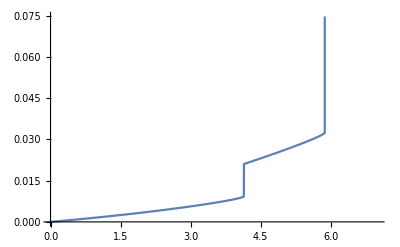

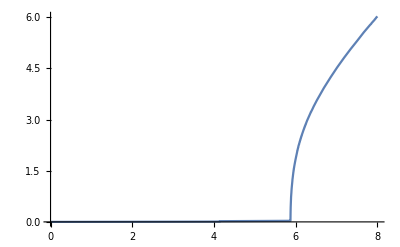

```mathematica
(*Вот те самые артефакты о которых я говорил по телефону ниже критического тока. Предыдущий рисунок разрывный именно как раз благодаря том что некоторые точки попадали в эту область. На следующем рисунке все уже становится впорядке.*)
Plot[{v[j,(Sin[#]+a Sin[c#+ϕ]+d Sin[f#+ϕ])&]},{j,0,7}]
Plot[{v[j,(Sin[#]+a Sin[c#+ϕ]+d Sin[f#+ϕ])&]},{j,0,8}]
```

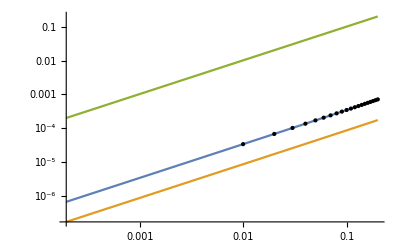

-5.61855+1.02106 x

```mathematica
Clear[j0];j0=5.468894080959671;
cprFunc0=(Sin[#]+1Sin[2#+π/3]+4 Sin[3#+π/3])&;
vx[j_]:=v[j-1,Sin];
vy[j_]:=v[j,cprFunc0];
LogLogPlot[{vx[j+1],vy[j],1.0210598649471812 j},{j,0,0.2},Epilog->{PointSize[Medium],Point[#]&/@Table[{Log[j],Log[vx[j+1]]},{j,0.01,0.2,0.01}]}]
Fit[Table[{Log[j],Log[vx[j+1]]},{j,0.01,0.2,0.01}],{1,x},x]
```

{{-7.51126,0.213392},{-6.81812,0.286377},{-6.41265,0.359281},{-6.12497,0.395869},{-5.90183,0.432531},{-5.7195,0.469333},{-5.56535,0.505667},{-5.43182,0.542043},{-5.31404,0.57851},{-5.20868,0.614982}}

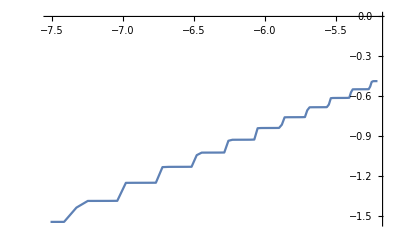

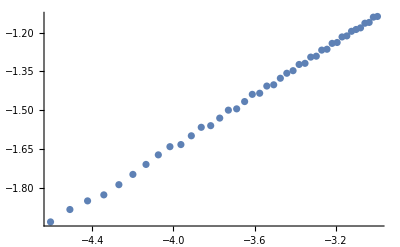

0.366753+0.501652 j

```mathematica
Table[{Log[j-j0],vy[j]},{j,j0+0.0001j0,j0+0.001j0,0.0001j0}]
ListLinePlot[Table[{Log[j-j0],Log[vy[j]]},{j,j0+0.0001j0,j0+0.001j0,0.00001j0}]]
ListPlot[Table[{Log[j-1], Log[v[j,Sin]]},{j,1.01,1.05,0.001}]]
Fit[Table[{Log[j-1], Log[v[j,Sin]]},{j,1.01,1.05,0.001}],{1,j},j]
```

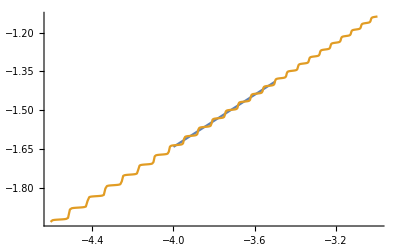

0.368622+0.502276 j

```mathematica
ListLinePlot[{Table[{j,0.3686215318311359+0.5022763858277515 j},{j,-4,-3.5,0.5}],Table[{Log[j-1], Log[v[j,Sin]]},{j,1.01,1.05,0.0001}]}]
Fit[Table[{Log[j-1], Log[v[j,Sin]]},{j,1.01,1.05,0.0001}],{1,j},j]
```

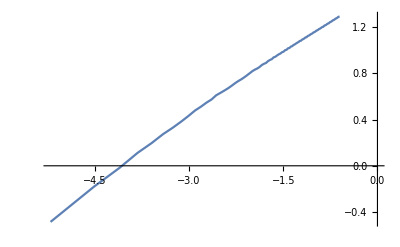

1.53522+0.369687 j

1.53522

0.369687

```mathematica
Clear[j0];j0=5.468894080959671;
ListLinePlot[Table[{Log[j-j0], Log[vy[j]]},{j,j0+0.001j0,j0+0.1j0,0.001j0}]]
Clear[fit];fit=Fit[Table[{Log[j-j0], Log[vy[j]]},{j,j0+0.001j0,j0+0.1j0,0.001j0}],{1,j},j]
Clear[b];b=fit/.j->0
Clear[k]; k=(fit-b)/.j->1
```

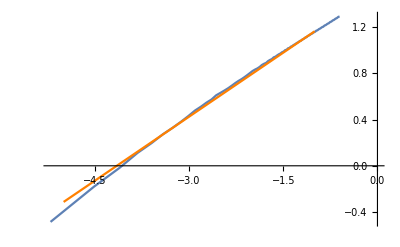

```mathematica
Show[-Graphics-,Plot[fit,{j,-5,-1},PlotStyle->Orange]]
```

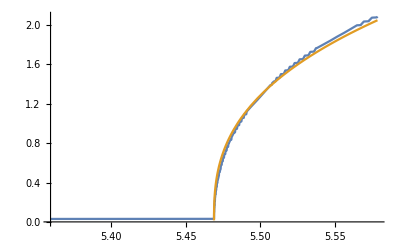

```mathematica
Plot[{vy[j],(Exp[b/k](j-j0))^k},{j,j0-0.02j0,j0+0.02j0}]
```

```mathematica
(*Заготовка для функции которая считает показатель степени при произвольной ток-фазе*)
```

```mathematica
(*GetIndex[cprFunc_]:=Module[{j0,fit,k,b,ctrlPlot},
j0=FindRoot[v[j,cprFunc]==0.001,{j,0.}]
ctrlPlot=Plot[v[j,cprFunc],{j,j0-0.1j0,j0+0.1j0}];
fit=Fit[Table[{Log[j-j0],Log[v[j, cprFunc]]},{j,j0+0.01j0,j0+0.1j0,0.01j0}],{1,j},j];
b=fit/.j->0;
k=(fit-b)/.j->1;
{Show[{ctrlPlot,Plot[Exp[b](j-j0)^k,,{j,j0-0.1j0,j0+0.1j0},PlotStyle->Orange]}],k}];*)
```

```mathematica
Clear[cprFunc1];cprFunc1=(Sin[#]+Sin[2#])&;
Clear[v1];v1[j_]:=v[j,cprFunc1];
```

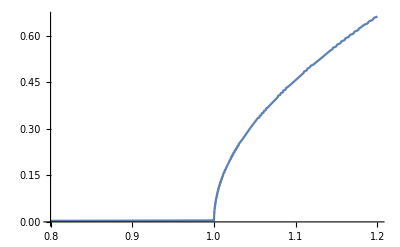

```mathematica
Plot[v[j,Sin],{j,1-0.2,1+0.2}]
```

```mathematica
Clear[indexes];indexes={{1,0.4778076072419194},{0.5,0.4841015841176004},{0.3,0.48866420178225084},{0.2,0.4918799070274129},{0.1,0.49454211652113855},{0.05,0.4962112331305276},{0.01,0.49950130038909774},{0,0.4984798362635317},{1.5,0.4739420504303039},{2,0.4702981329756268},{2.5,0.4671161900318918},{3,0.46497710434865275},{3.5,0.4621962850340193},{4,0.45992815848549384},{4.5,0.45828519627015046},{5,0.45607882892552176},{5.5,0.4544057986979846},{6,0.45275653624037604},{6.5,0.4512548809577924},{7,0.449849874193609},{10,0.4420793344049469},{30,0.41400850700914094},{50,0.4005368982312128}};
```

```mathematica
Clear[a];a=100000;
Clear[sol];sol:=ParametricNDSolve[Diffur[γ,t,((1/a)Sin[#]+Sin[2#+π/3])&,ccur,0,0],γ[t],{t,0,3000π},ccur]
Clear[u];u[j_?NumericQ]:=(1/3000π)(γ[t]/.sol)[j]/.t->3000π;
```

```mathematica
Clear[j0];j0=j/.FindRoot[u[j]==0.01,{j,2}];
j0
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.00001

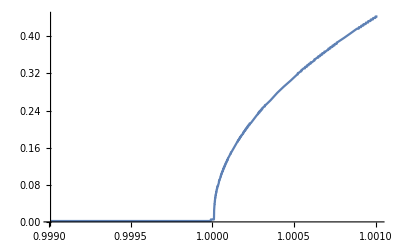

```mathematica
Clear[ctrlPlot];ctrlPlot=Plot[u[j],{j,j0-0.001j0,j0+0.001j0}]
```

```mathematica
Clear[fit];fit=Fit[Table[{Log[j-j0],Log[u[j]]},{j,j0+0.001j0,j0+0.01j0,0.001j0}],{1,j},j]
```

2.63712+0.499729 j

```mathematica
Clear[b];b=fit/.j->0;

Clear[k];k=(fit-b)/.j->1;
```

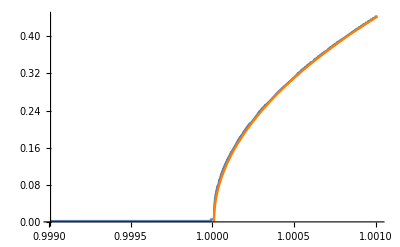

```mathematica
Show[ctrlPlot,Plot[Exp[b](j-j0)^k,{j,j0-0.001j0,j0+0.001j0},PlotStyle->Orange]]
```

```mathematica
AppendTo[indexes,{a,k}]
```

```mathematica
indexes=
```

{{1,0.477808},{0.5,0.484102},{0.3,0.488664},{0.2,0.49188},{0.1,0.494542},{0.05,0.496211},{0.01,0.499501},{0,0.49848},{1.5,0.473942},{2,0.470298},{2.5,0.467116},{3,0.464977},{3.5,0.462196},{4,0.459928},{4.5,0.458285},{5,0.456079},{5.5,0.454406},{6,0.452757},{6.5,0.451255},{7,0.44985},{10,0.442079},{30,0.414009},{50,0.400537},{100,0.385501},{1000,0.420906},{10000,0.484326},{100000,0.499729}}

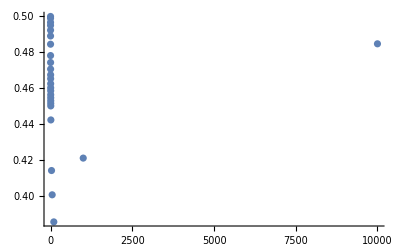

```mathematica
ListPlot[Delete[indexes,-1],PlotRange->All]
```

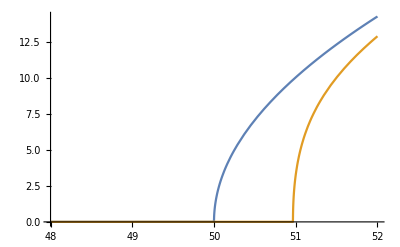

```mathematica
Plot[{v[j,50Sin[2#+π/3]&],v[j,(Sin[#]+50Sin[2#+π/3])&]},{j,50-2,50+2}]
```

```mathematica
AppendTo
```